## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"]
```

```mathematica
N[AlphaNS[6,η[30,40],0.09,-0.3]*Pi^2]
```

-11958.9

```mathematica
N[AlphaS[6,η[30,40],0.09,-0.3]*Pi^2]
```

-1398.45

```mathematica
N[AlphaLNS[6,η[30,40],0.09,-0.3]*Pi^2]
```

-1072.81

```mathematica
N[AlphaLS[6,η[30,40],0.09,-0.3]*Pi^2]
```

0.

```mathematica
N[AlphaL[6,η[30,40],0.09,-0.3]*Pi^2]
```

-1072.81

```mathematica
-1072.8103323596813
```

```mathematica
N[Alpha[6,η[30,40],0.09,-0.3]*Pi^2]
```

-13357.4

```mathematica
timeMetric 70
```

0.00034478436633488868847380606489488653

```mathematica
N[Alpha[6,η[30,40],0.09,-0.3]+AlphaL[6,η[30,40],0.09,-0.3]Log[π timeMetric 70]] Pi^2
```

-6032.38

```mathematica
N[TimeMetricOneThirds[6-5]CE[η[30,40]]PiMOneThirds[6-5,70]]/Pi^2
```

0.000995846

```mathematica
N[Psi["6l",η[33,12],M[33,12],0.8,0.57]]
```

```mathematica
-1.1546977026861354
```

-1.1547

```mathematica
N[Psi[6,η[33,12],M[33,12],0.8,0.57]]
```

14.6419

```mathematica
14.641858124785827
```

```mathematica
-1.1546977026861354
```

```mathematica
N[Psi[3,η[33,12],M[33,12],0.8,0.57]]
```

-394.146

```mathematica
N[Psi[4,η[33,12],M[33,12],0.8,0.57]]
```

20.1133

```mathematica
20.11334056036653
```

```mathematica
N[Psi[7,η[33,12],M[33,12],0.8,0.57]]
```

-3.60265

```mathematica
-3.602648446577167
```

```mathematica
N[Psi[0,η[33,12],M[33,12],0.8,0.57]]
```

21908.9

```mathematica
21908.934774088466
```

```mathematica
N[Psi[1,η[33,12],M[33,12],0.8,0.57]]
```

0.

```mathematica
0.
```

0.

```mathematica
N[Psi[2,η[33,12],M[33,12],0.8,0.57]]
```

1051.49

```mathematica
1051.4901921172077
```

```mathematica
N[Psi["5l",η[33,12],M[33,12],0.8,0.57]]
```

-4.98885

```mathematica
-4.988853401753867
```

```mathematica
N[Psi[6,η[33,12],M[33,12],0.8,0.57]]
```

14.6419

```mathematica
14.641858124785827
```

```mathematica
15.96367509417229
```

15.9637

```mathematica
14.641858124785827
```

```mathematica
N[LALSimPhi[3,η[33,12],0.8,0.57]](3-5)/5
```

32.4664

## Gw@150914!

```mathematica
N[(99*99)/(99+99)^2]
```

0.25

## 设置non-GR参数字符flag

```mathematica
eventFlag="GW150914";
psiFlag="psi";
alphaFlag="alpha";

deviationFlag="cpsi";
deviationOrder=3;
deviationType="constant";

fileSuffix="";

alphaName=alphaFlag<>ToString[deviationOrder]
psiName=psiFlag<>ToString[deviationOrder]
deviationName=deviationFlag<>ToString[deviationOrder]
modifiedAlphaName=alphaFlag<>ToString[deviationOrder]<>deviationFlag
modifiedPsiName=psiFlag<>ToString[deviationOrder]<>deviationFlag
```

alpha3

psi3

cpsi3

alpha3cpsi

psi3cpsi

```mathematica
"alpha3"
```

alpha3

## Prepare Data from CSV or HDF

```mathematica
csvFolder="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv"<>"\\"<>eventFlag
csvName="OGC4-GW150914_"<>deviationName<>fileSuffix<>".csv"
csvPath=csvFolder<>"\\"<>csvName
```

D:\Documents\workspace\课题\workspace\Local\Parameterized_PN_Tests\csv\GW150914

OGC4-GW150914_cpsi3.csv

D:\Documents\workspace\课题\workspace\Local\Parameterized_PN_Tests\csv\GW150914\OGC4-GW150914_cpsi3.csv

### from CSV

```mathematica
CSVSamples=Import[csvPath];

samples=<||>;
samples["mass1"]=CSVSamples[[All,1]][[2;;]];
samples["mass2"]=CSVSamples[[All,2]][[2;;]];
samples["spin1_z"]=CSVSamples[[All,3]][[2;;]];
samples["spin2_z"]=CSVSamples[[All,4]][[2;;]];
samples["eta"]=CSVSamples[[All,5]][[2;;]];
samples["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[deviationName]=CSVSamples[[All,7]][[2;;]];
```

```mathematica
samples["chis"]=χs[samples["spin1_z"],samples["spin2_z"]];
samples["chia"]=χa[samples["spin1_z"],samples["spin2_z"]];
```

### Calculate Coefficients

#### N-Order Coefficients, ψ

```mathematica
samples["psi0"]=MapThread[
Psi[0,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi2"]=MapThread[
Psi[2,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi3"]=MapThread[
Psi[3,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi4"]=MapThread[
Psi[4,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi5"]=MapThread[
Psi[5,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi5l"]=MapThread[
Psi["5l",η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi6"]=MapThread[
Psi[6,η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
samples["psi6l"]=MapThread[
Psi["6l",η[#1,#2],M[#1,#2],#3,#4]&,
{samples["mass1"],samples["mass2"],samples["spin1_z"],samples["spin2_z"]}
];
```

```mathematica
Keys[samples]
```

{mass1,mass2,spin1_z,spin2_z,eta,Mchirp,cpsi3,chis,chia,psi0,psi2,psi3,psi4,psi5,psi5l,psi6,psi6l}

```mathematica
samples["psi6l"]
```

## Plot PN Coefficients and Related Parameters

```mathematica
BCI=<||>;
```

### Plots Masses

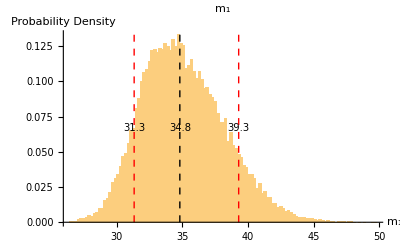

```mathematica
BCI["mass1"]=PlotParameterWithBCI[samples["mass1"],Subscript["m","1"]][[1]];
```

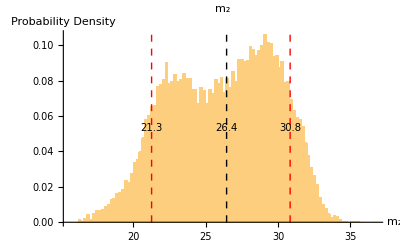

```mathematica
BCI["mass2"]=PlotParameterWithBCI[samples["mass2"],Subscript["m","2"]][[1]];
```

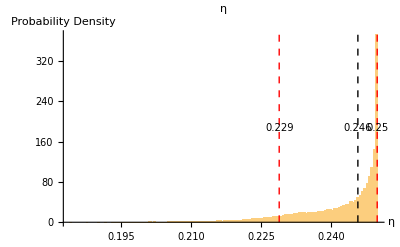

```mathematica
BCI["eta"]=PlotParameterWithBCI[samples["eta"],"η"][[1]];
```

### Plots Spin Components Aligning Orbital Angular Momentum (Then be it spin_z)

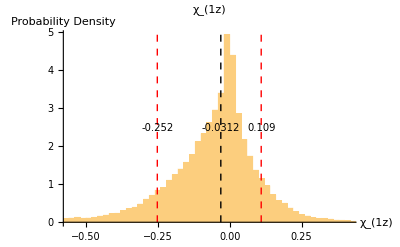

```mathematica
BCI["spin1_z"]=PlotParameterWithBCI[samples["spin1_z"],Subscript["χ","1z"]][[1]];
```

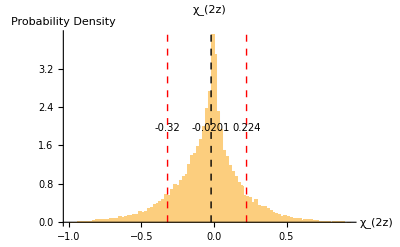

```mathematica
BCI["spin2_z"]=PlotParameterWithBCI[samples["spin2_z"],Subscript["χ","2z"]][[1]];
```

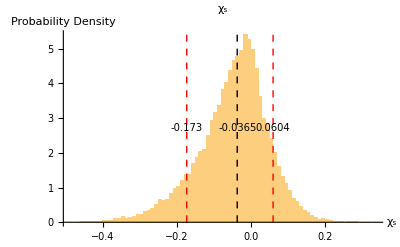

```mathematica
BCI["chis"]=PlotParameterWithBCI[samples["chis"],Subscript["χ","s"]][[1]];
```

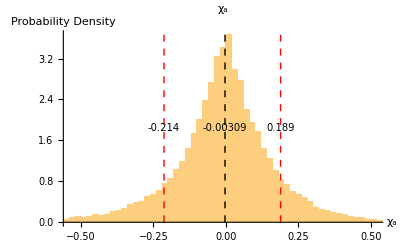

```mathematica
BCI["chia"]=PlotParameterWithBCI[samples["chia"],Subscript["χ","a"]][[1]];
```

### Plot psi

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

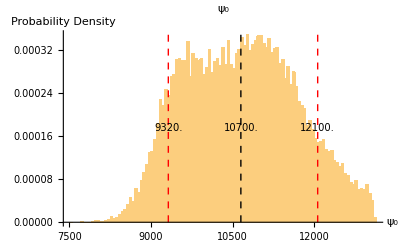

```mathematica
BCI["psi0"]=PlotParameterWithBCI[samples["psi0"],Subscript["ψ","0"]][[1]];
```

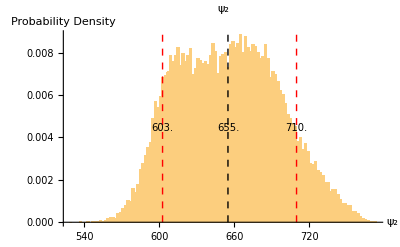

```mathematica
BCI["psi2"]=PlotParameterWithBCI[samples["psi2"],Subscript["ψ","2"]][[1]];
```

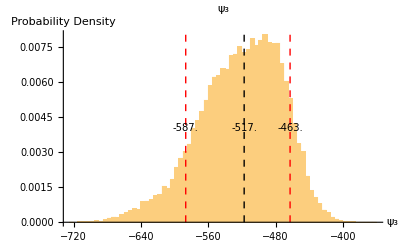

```mathematica
BCI["psi3"]=PlotParameterWithBCI[samples["psi3"],Subscript["ψ","3"]][[1]];
```

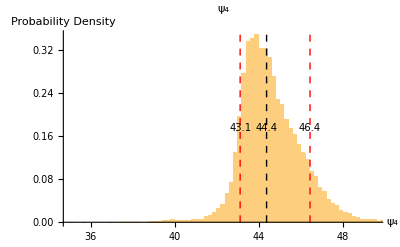

```mathematica
BCI["psi4"]=PlotParameterWithBCI[samples["psi4"],Subscript["ψ","4"]][[1]];
```

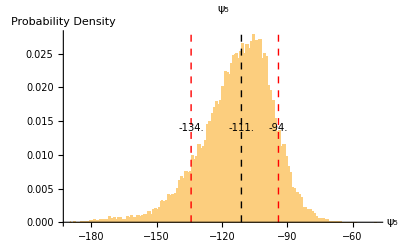

```mathematica
BCI["psi5"]=PlotParameterWithBCI[samples["psi5"],Subscript["ψ","5"]][[1]];
```

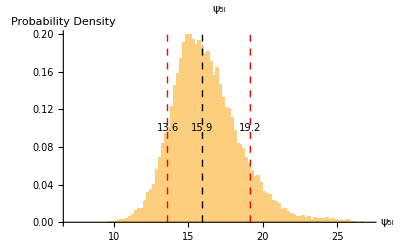

```mathematica
BCI["psi5l"]=PlotParameterWithBCI[samples["psi5l"],Subscript["ψ","5l"]][[1]];
```

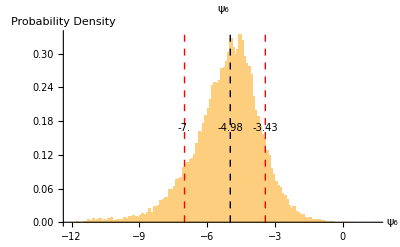

```mathematica
BCI["psi6"]=PlotParameterWithBCI[samples["psi6"],Subscript["ψ","6"]][[1]];
```

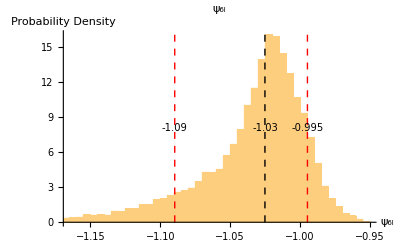

```mathematica
BCI["psi6l"]=PlotParameterWithBCI[samples["psi6l"],Subscript["ψ","6l"]][[1]];
```

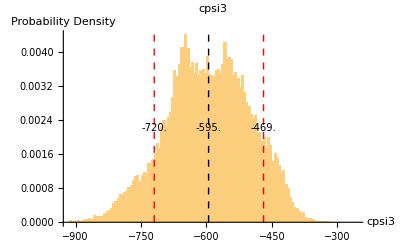

```mathematica
BCI[deviationName]=PlotParameterWithBCI[samples[deviationName],deviationName][[1]];
```

```mathematica
Keys[samples]
```

{mass1,mass2,spin1_z,spin2_z,eta,Mchirp,cpsi3,chis,chia,psi0,psi2,psi3,psi4,psi5,psi5l,psi6,psi6l}

```mathematica
Mean[samples[deviationName]]
```

-595.623

```mathematica
StandardDeviation[samples[deviationName]]
```

95.7408

```mathematica
{BCI["mass1"],BCI["mass2"]}
```

{{31.3289,34.8102,39.2947},{21.2699,26.4486,30.8345}}

```mathematica
{BCI["mass1"][[2]],BCI["mass2"][[1]]}
```

{34.8102,21.2699}

```mathematica
BCI[deviationName]=BCI[deviationName]~Append~Psi[3,η[BCI["mass1"][[2]],BCI["mass2"][[1]]],M[BCI["mass1"][[2]],BCI["mass2"][[1]]],BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]]
```

{-719.716,-595.071,-469.082,-559.486}

```mathematica
(BCI[deviationName]-Mean[samples[deviationName]])/StandardDeviation[samples[deviationName]]
```

{-1.29613,0.00576244,1.32171,0.377445}

## Intersection

```mathematica
(*定义一个示例函数曲面*)surface=
Plot3D[
Function[{m1,m2},Psi[deviationOrder,η[m1,m2],M[m1,m2],BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]]][m1,m2],
{m1,20,100},
{m2,20,100},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=158.7,Red,Blue]&),
ColorFunctionScaling->False,
PlotStyle->{Opacity[0.6]},
PlotRange->All
];

(*定义z=0.5的常数平面*)
constantPlane1=Plot3D[BCI[deviationName][[1]],{x,20,100},{y,20,100},PlotStyle->{Opacity[0.3],Blue},Mesh->None];
constantPlane2=Plot3D[BCI[deviationName][[2]],{x,20,100},{y,20,100},PlotStyle->{Opacity[0.3],Blue},Mesh->None];
constantPlane3=Plot3D[BCI[deviationName][[3]],{x,20,100},{y,20,100},PlotStyle->{Opacity[0.3],Blue},Mesh->None];

constantPlaneGR2=Plot3D[BCI[psiName][[2]],{x,20,100},{y,20,100},PlotStyle->{Opacity[0.3],Blue},Mesh->None];

(*组合显示两个图形*)
Show[surface,constantPlane1,constantPlane2,constantPlane3,constantPlaneGR2,PlotLabel->"3D曲面与z=0.5常数平面",AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
BCI
```

<|mass1→{30.9292,35.9022,41.9551},mass2→{21.7115,25.2133,29.6095},eta→{0.224863,0.242372,0.249863},spin1_z→{-0.0351468,0.128829,0.307007},spin2_z→{-0.162377,0.0453091,0.307097},chis→{0.0493944,0.0838265,0.174359},chia→{-0.159018,0.0424662,0.227298},psi0→{10129.3,10611.7,11003.9},psi2→{634.021,654.956,671.916},psi3→{-482.76,-474.126,-463.384},psi6l→{-1.12739,-1.03201,-0.995462},cpsi3→{-209.728,-205.817,-197.828}|>

## Calculate Dots

IMRPhenomXPHM

### 2D, m_1-m_2, Fix two spin parameters

#### Set m_2-m_1 Axis

```mathematica
m1s=Range[BCI["mass2"][[1]]-10,BCI["mass2"][[3]]+10,0.1];
m2s=Range[BCI["mass1"][[1]]-10,BCI["mass1"][[3]]+10,0.1];
```

```mathematica
m1s=Range[10,80,0.1];
m2s=Range[10,80,0.1];
```

```mathematica
m1s=Range[30,70,1];
m2s=Range[30,70,1];
```

## Construct tape borders

```mathematica
List[]
```

{}

```mathematica
plots=List[]
For[i=0,i<5,i++,
pInterval=IntervalFromProbability[0.0+i*0.19/3];
tapeIntervals=<||>;
tapes=<||>;
tapeIntervals["mass1"]=Quantile[samples["mass1"],pInterval];
tapeIntervals["mass2"]=Quantile[samples["mass2"],pInterval];

Quiet[
tapeIntervals["psi0"]=Quantile[samples["psi0"],pInterval];
tapes["psi0"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals["psi0"],{m2s},{2},{0,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},tapeIntervals["mass2"],2];

tapeIntervals["psi2"]=Quantile[samples["psi2"],pInterval];
tapes["psi2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals["psi2"],{m2s},{2},{2,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},tapeIntervals["mass2"],2];

tapeIntervals[deviationName]=Quantile[samples[deviationName],pInterval];
tapes[deviationName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[deviationName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},tapeIntervals["mass2"],2];
];

AppendTo[plots,ListLinePlot[
{
(*Labeled[tapes["psi0"][[1]][[2;;]],Subscript["ψ","0"]],
Labeled[tapes["psi0"][[2]][[2;;]],Subscript["ψ","0"]],

Labeled[tapes["psi2"][[1]][[2;;]],Subscript["ψ","2"]],
Labeled[tapes["psi2"][[2]][[2;;]],Subscript["ψ","2"]],

Labeled[tapes[deviationName][[1]][[2;;]],psiName<>" "<>ToString[pInterval[[1]]*100]<>"% BCI, observed"],
Labeled[tapes[deviationName][[2]][[2;;]],psiName<>" "<>ToString[pInterval[[2]]*100]<>"% BCI, observed"]*)

tapes["psi0"][[1]][[2;;]],
tapes["psi0"][[2]][[2;;]],

tapes["psi2"][[1]][[2;;]],
tapes["psi2"][[2]][[2;;]],

tapes[deviationName][[1]][[2;;]],
tapes[deviationName][[2]][[2;;]]
},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{HatchFilling["Diagonal"]},
AxesLabel->{Subscript["m","1"],Subscript["m","2"]},
AspectRatio->1(*,
PlotLegends->{1,2,3,4,5,6,7}*),
PlotRange->{{30,70},{10,30}}
]
]
]
```

{}

```mathematica
Grid[{
{Style["Expansion of probability tapes with incrementing p"]},
{GraphicsRow[
plots,
PlotLabel->"12412134"
]},
{
Graphics[{(*坐标轴线条*)Line[{{0,0},{10,0}}],(*坐标轴箭头*)Arrow[{{10,0},{11,0}}],(*刻度线和刻度标签*)Table[{Line[{{i,-0.2},{i,0.2}}],(*刻度线*)Text[i,{i,-0.5},{0,1}]    (*刻度标签*)},{i,0,10,2}  (*从0到10，间隔为2的刻度*)],(*轴标签 "p"*)Text[Style["p",14,Bold],{11.5,0},{0,0}]},PlotRange->{{-1,12},{-1,1}},(*控制显示范围*)AspectRatio->1/8,(*宽高比，使坐标轴更修长*)ImageSize->400                   (*图像宽度*)]
}
}
]
```

Expansion of probability tapes with incrementing p
-Graphics-
-Graphics-

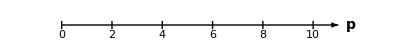

```mathematica
Graphics[{(*坐标轴线条*)Line[{{0,0},{10,0}}],(*坐标轴箭头*)Arrow[{{10,0},{11,0}}],(*刻度线和刻度标签*)Table[{Line[{{i,-0.2},{i,0.2}}],(*刻度线*)Text[i,{i,-0.5},{0,1}]    (*刻度标签*)},{i,0,10,2}  (*从0到10，间隔为2的刻度*)],(*轴标签 "p"*)Text[Style["p",14,Bold],{11.5,0},{0,0}]},PlotRange->{{-1,12},{-1,1}},(*控制显示范围*)AspectRatio->1/8,(*宽高比，使坐标轴更修长*)ImageSize->400                   (*图像宽度*)]
```

```mathematica
HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals["psi2"],{m2s},{2},{2,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},tapeIntervals["mass2"],2]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{{30,31.7621},{31,30.7247},{32,29.7844},{33,28.9282},{34,28.1454},{35,27.427},{36,26.7655},{37,26.1545},{38,25.5886},{39,25.0629},{40,24.5736},{41,24.117},{42,23.69},{43,23.29},{44,22.9145},{45,22.5614},{46,22.2288},{47,21.9151},{48,21.6186},{49,21.3382},{50,21.0725},{51,20.8205},{52,20.5812},{53,20.3536},{54,20.137},{55,19.9306},{56,19.7336},{57,19.5456},{58,19.3659},{59,19.194},{60,19.0294},{61,18.8717},{62,18.7205},{63,18.5753},{64,18.4359},{65,18.3018},{66,18.1729},{67,18.0488},{68,17.9293},{69,17.8142},{70,17.7031},{71,17.5959},{72,17.4924},{73,17.3924},{74,17.2958},{75,17.2023},{76,17.1119},{77,17.0244},{78,16.9396},{79,16.8574},{80,16.7778}},{{30,27.8007},{31,26.9527},{32,26.1817},{33,25.4778},{34,24.8328},{35,24.2396},{36,23.6923},{37,23.186},{38,22.7164},{39,22.2796},{40,21.8724},{41,21.4921},{42,21.1361},{43,20.8022},{44,20.4886},{45,20.1934},{46,19.9151},{47,19.6524},{48,19.404},{49,19.1689},{50,18.946},{51,18.7344},{52,18.5333},{53,18.342},{54,18.1598},{55,17.9861},{56,17.8204},{57,17.662},{58,17.5105},{59,17.3656},{60,17.2268},{61,17.0937},{62,16.966},{63,16.8434},{64,16.7255},{65,16.6123},{66,16.5032},{67,16.3983},{68,16.2971},{69,16.1996},{70,16.1055},{71,16.0147},{72,15.927},{73,15.8422},{74,15.7602},{75,15.6809},{76,15.6042},{77,15.5299},{78,15.4579},{79,15.3881},{80,15.3204}}}

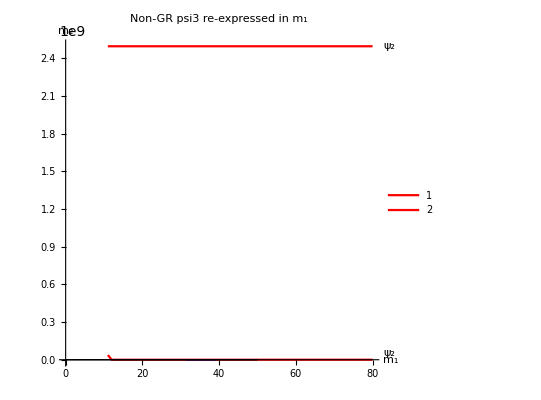

```mathematica
ListLinePlot[
{


Labeled[tapes["psi2"][[1]][[2;;]],Subscript["ψ","2"]],
Labeled[tapes["psi2"][[2]][[2;;]],Subscript["ψ","2"]]

},
PlotStyle->{Red,Red,Green,Green,Purple,Purple},

FillingStyle->{HatchFilling["Diagonal"]},
Epilog->{
Blue,Line[{{BCI["mass1"][[2]],BCI["mass2"][[1]]},{BCI["mass1"][[2]],BCI["mass2"][[3]]}}],
Blue,Line[{{BCI["mass1"][[1]],BCI["mass2"][[2]]},{BCI["mass1"][[3]],BCI["mass2"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","1"],Subscript["m","2"]},
AspectRatio->1,
PlotLegends->{1,2,3,4,5,6,7}
]
```

#### ψ_0 and ψ_2 Pancakes

```mathematica
pancakes=<||>;
```

```mathematica
BCI["psi0"]
```

{9318.89,10653.7,12067.2}

```mathematica
pancakes["psi0"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi0"],{m2s},{2},{0,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes["psi2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi2"],{m2s},{2},{2,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes[psiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

#### ψ_0 and ψ_2 Non-GR Pancakes

```mathematica
pancakes[deviationName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[deviationName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"]~Append~BCI["mass2"][[]],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

#### ψ_0 and ψ_2 Pancakes

```mathematica
tapes=<||>;
```

```mathematica
BCI["psi0"]
```

{9318.89,10653.7,12067.2}

```mathematica
pancakes["psi0"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi0"],{m2s},{2},{0,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes["psi2"]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI["psi2"],{m2s},{2},{2,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakes[psiName]=HypersurfacePancake[Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
BCI[psiName],{m2s},{2},{deviationOrder,BCI["spin1_z"][[2]],BCI["spin2_z"][[2]]},BCI["mass2"],2];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

#### Plots

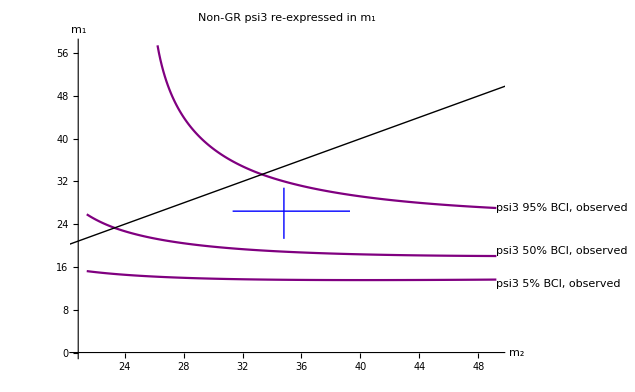

```mathematica
ListLinePlot[
{
Labeled[pancakes[deviationName][[1]][[2;;]],psiName<>" 5% BCI, observed"],
Labeled[pancakes[deviationName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakes[deviationName][[3]][[2;;]],psiName<>" 95% BCI, observed"]
},
PlotStyle->{Purple},
Epilog->{
Blue,Line[{{BCI["mass1"][[2]],BCI["mass2"][[1]]},{BCI["mass1"][[2]],BCI["mass2"][[3]]}}],
Blue,Line[{{BCI["mass1"][[1]],BCI["mass2"][[2]]},{BCI["mass1"][[3]],BCI["mass2"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","2"],Subscript["m","1"]}
]
```

```mathematica
ListLinePlot[
{
Labeled[pancakes["psi0"][[1]][[2;;]],Subscript["ψ","0"]],
Labeled[pancakes["psi0"][[3]][[2;;]],Subscript["ψ","0"]],

Labeled[pancakes["psi2"][[1]][[2;;]],Subscript["ψ","2"]],
Labeled[pancakes["psi2"][[3]][[2;;]],Subscript["ψ","2"]],
(*Labeled[pancakes[psiName][[2]][[2;;]],psiName],*)

Labeled[pancakes[deviationName][[1]][[2;;]],psiName<>" 5% BCI, "],
Labeled[pancakes[deviationName][[2]][[2;;]],psiName<>" 50% BCI, observed"],
Labeled[pancakes[deviationName][[4]][[2;;]],psiName<>" 62.56% BCI, observed"],
Labeled[pancakes[deviationName][[3]][[2;;]],psiName<>" 95% BCI, observed"]
},
PlotStyle->{Red,Red,Green,Green,Purple,Purple,Purple,Purple},
Filling->{1->{2},3->{4},5->{7}},
FillingStyle->{HatchFilling["Diagonal"]},
Epilog->{
Blue,Line[{{BCI["mass1"][[2]],BCI["mass2"][[1]]},{BCI["mass1"][[2]],BCI["mass2"][[3]]}}],
Blue,Line[{{BCI["mass1"][[1]],BCI["mass2"][[2]]},{BCI["mass1"][[3]],BCI["mass2"][[2]]}}],
Black,Line[{{0,0},{50,50}}]
	},
PlotLabel->"Non-GR "<>psiName<>" re-expressed in "Subscript["m","1"],
AxesLabel->{Subscript["m","1"],Subscript["m","2"]},
AspectRatio->1,
PlotLegends->{1,2,3,4,5,6,7}
(*PlotRange->{{1,60},{1,60}}*)
]
```

-Graphics-

```mathematica
(BCI[deviationName]-Mean[samples[deviationName]])/StandardDeviation[samples[deviationName]]
```

{-1.29613,0.00576244,1.32171,0.377445}

```mathematica
(BCI[deviationName]-samples[psiName][[2]])/StandardDeviation[samples[psiName]]
```

{-3.86869,-1.31972,1.25676,-0.592006}

```mathematica
(*定义百分位数计算函数*)
PercentileRank[data_,x_]:=Module[{countLess,total},countLess=Count[data,_?(#<x&)];(*统计小于x的元素数*)total=Length[data];(*总元素数*)If[total==0,0,N[(countLess/total)*100]]  (*避免除以0*)]

(*测试函数*)
data={3,1,4,1,5,9,2,6};
x=5;
PercentileRank[data,x]  (*结果：62.5，表示5大于62.5%的元素*)
```

62.5

```mathematica
PercentileRank[samples[deviationName],BCI[deviationName][[4]]]
```

62.5565

```mathematica
ArcSin[π/(19/2^7)^(1/2)/4.]
```

1.5708-1.33893 ⅈ

```mathematica
π/(19/2^7)^(1/2)/4.
```

2.03853

### 3D, χ_s-χ_a-η

```mathematica
chiss=Range[BCI["chis"][[1]],BCI["chis"][[2]],1/50];
chias=Range[BCI["chia"][[1]],BCI["chia"][[2]],1/50];
```

```mathematica
pancakes[alphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[alphaName],(* F0_ *)
{chiss,chias},{2,3},(* axes_,axesIndices_ *)
{deviationOrder},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Select[Flatten[pancakes[alphaName][[1]],Depth=1],Im[#[[3]]]==0 &];
```

Set::wrsym: Symbol Depth is Protected.

```mathematica
ListPlot3D[
{
Select[Flatten[pancakes[alphaName][[1]],Depth=1],Im[#[[3]]]==0 &]
(*,Select[Flatten[pancakes[alphaName][[2]],Depth=1],Im[#[[3]]]==0 &]*)
(*,Select[Flatten[pancakes[alphaName][[3]],Depth=1],Im[#[[3]]]==0 &]*)
},
PlotRange->{{BCI["chis"][[1]],BCI["chis"][[3]]},{BCI["chia"][[1]],BCI["chia"][[3]]},{BCI["eta"][[1]],BCI["eta"][[3]]}}
]
```

Set::wrsym: Symbol Depth is Protected.

-Graphics3D-

```mathematica
pancakesFixChia[alphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[alphaName],(* F0_ *)
{chiss},{2},(* axes_,axesIndices_ *)
{deviationOrder,BCI["chia"][[2]]},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
pancakesFixChia[modifiedAlphaName]=HypersurfacePancake[
Function[{j,eta,chis,chia},
Alpha[j,eta,χ1L[chis,chia],χ2L[chis,chia]]],(* F_ *)
BCI[modifiedAlphaName],(* F0_ *)
{chiss},{2},(* axes_,axesIndices_ *)
{deviationOrder,BCI["chia"][[2]]},(* FArgs_ *)
BCI["eta"],2(* h0_,hIndex_ *)
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
pancakesFixChia[modifiedAlphaName]
```

{{{-0.176261,-2.23601},{-0.156261,-2.63373},{-0.136261,-3.13345},{-0.116261,-3.78142},{-0.0962614,-4.65754},{-0.0762614,-5.91358},{-0.0562614,-7.88009}},{{-0.176261,-0.515673},{-0.156261,-0.705506},{-0.136261,-0.942205},{-0.116261,-1.24574},{-0.0962614,-1.64989},{-0.0762614,-2.21694},{-0.0562614,-3.07708}},{{-0.176261,0.287298+3.5425×10^-15 ⅈ},{-0.156261,0.280539+2.72387×10^-15 ⅈ},{-0.136261,0.273704+3.80329×10^-15 ⅈ},{-0.116261,0.26679+2.26418×10^-15 ⅈ},{-0.0962614,0.259798+3.88682×10^-15 ⅈ},{-0.0762614,0.252725+1.98253×10^-15 ⅈ},{-0.0562614,0.22858}}}

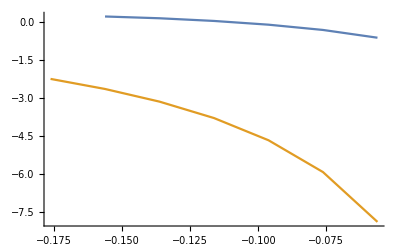

```mathematica
ListLinePlot[
{
Select[pancakesFixChia[alphaName][[1]],Im[#[[2]]]==0 &],
Select[pancakesFixChia[modifiedAlphaName][[1]],Im[#[[2]]]==0 &],
Select[pancakesFixChia[modifiedAlphaName][[3]],Im[#[[2]]]==0 &]
}
(*,PlotRange->{{-0.3,0},{0,1/4}}*)
]
```